# 1. izpit – Mathematica

## Računalniški praktikum 2023/24

Študijske smeri: Matematika, Pedagoška matematika

## Podatki o študentu

Vpišite svoje podatke

Ime: Kanisaja Nika

Priimek: Kovačič

Vpisna številka: 27241037

## Navodila

Čas reševanja za celoten izpit je 120 minut.
V tem delu izpita so tri naloge, ki so skupaj vredne 30 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.
Dovoljeno je uporabljati dokumentacijo o Mathematici in gradivo iz vaj.
Vsakršna komunikacija je prepovedana.

## 1. naloga [5 točk]

Izračunajte limito .

```mathematica
Limit[(1000^n+1024^n.08)^(1/n),n->Infinity]
```

ConditionalExpression[1024, .08>0]

## 2. naloga [15 točk]

Na neki točki boste spoznali Taylorjev razvoj eksponentne funkcije. Eksponentno funkcijo lahko namreč zapišemo kot funkcijsko potenčno vrsto oblike . Ta zapis nam pove, da lahko z delnimi vsotami  poljubno dobro aproksimiramo eksponentno funkcijo.
1. (5 točk) Izračunajte numerično vrednost delne vsote . Uporabite lahko funkcijo Factorial. Če želite, lahko prej definirate funkcijo iz naslednje naloge in jo uporabite.
2. (5 točk) Definirajte funkcijo delne vsote fn, ki sprejme parametra x in n in ima zgornji predpis. Funkcija naj vrača točne vrednosti, ne numeričnih približkov.
3. (5 točk) Narišite grafa eksponentne funkcije in tretje delne vsote na intervalu [-3,3] . Pri tem nastavite razmerje koordinatnih osi na automatic in zalogo vrednosti na [0,7].

1.06059

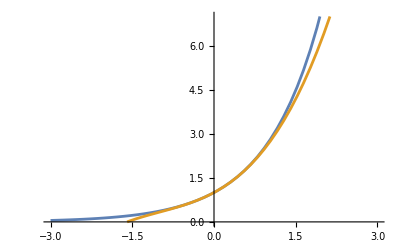

```mathematica
N[Sum[17^(-k)/Factorial[k],{k,0,17}]]
fn[x_,n_]:= Sum[x^(k)/Factorial[k],{k,0,n}]
Plot[{E^x,fn[x,3]},{x,-3,3}, PlotRange->{0,7}, AspectRatio->Automatic]
```

```mathematica
N[156033164739869431839851994830935409/147119480583906308566523998058496000]
```

1.06059

## 3. naloga [10 točk]

1. (5 točk) Definirajte funkcijo PetQ, ki sprejme parameter n in vrne True, če ima n natanko 5 deliteljev.
2. (5 točk) Izpišite vsa števila med 1 in 1000, ki imajo natanko 5 deliteljev.

```mathematica
f[n_] := Length[Divisors[n]]==5
Select[Range[1000],f]
f[5]
```

{16,81,625}

False